## Chapter 4 [Systems of ODEs]

## 4.1 Solving A System of ODEs by DSolve, Initial Value Problem

```mathematica
Clear["Global`*"]
```

```mathematica
sys={y1'[t]==-3y1[t]+y2[t],y2'[t]==y1[t]-3y2[t]}
```

{y1'[t]==-3 y1[t]+y2[t],y2'[t]==y1[t]-3 y2[t]}

```mathematica
sys[[1]]
```

y1'[t]==-3 y1[t]+y2[t]

```mathematica
sys[[2]]
```

y2'[t]==y1[t]-3 y2[t]

```mathematica
sol=DSolve[sys,{y1[t],y2[t]},t]
```

{{y1[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2],y2[t]→1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
sol2=FullSimplify[sol]
```

{{y1[t]→ⅇ^(-3 t) (C[1] Cosh[t]+C[2] Sinh[t]),y2[t]→ⅇ^(-3 t) (C[2] Cosh[t]+C[1] Sinh[t])}}

```mathematica
FullSimplify[sol/.{C[1]->c1+c2,C[2]->c1-c2}]
```

{{y1[t]→ⅇ^(-4 t) (c2+c1 ⅇ^(2 t)),y2[t]→ⅇ^(-4 t) (-c2+c1 ⅇ^(2 t))}}

```mathematica
yp=DSolve[{sys[[1]],sys[[2]],y1[0]==1,y2[0]==5},{y1[t],y2[t]},t]
```

{{y1[t]→ⅇ^(-4 t) (-2+3 ⅇ^(2 t)),y2[t]→ⅇ^(-4 t) (2+3 ⅇ^(2 t))}}

```mathematica
f1=yp[[1]][[1,2]]
```

ⅇ^(-4 t) (-2+3 ⅇ^(2 t))

```mathematica
f2=yp[[1]][[2,2]]
```

ⅇ^(-4 t) (2+3 ⅇ^(2 t))

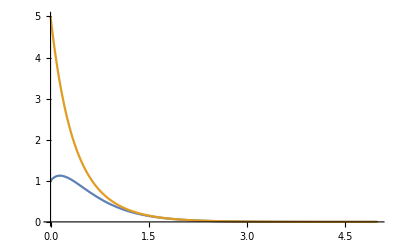

```mathematica
Plot[{f1,f2},{t,0,5},PlotRange->{0,5}]
```

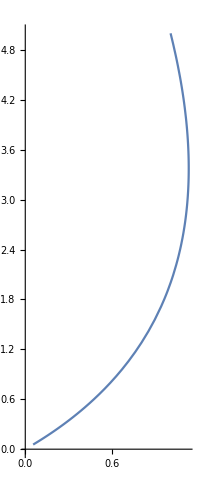

```mathematica
ParametricPlot[{f1,f2},{t,0,2}]
```

## 4.2 Use of Matrices in Solving Systems of ODEs

```mathematica
Clear[y1,y2]
```

```mathematica
sys={y1'[t]==-3y1[t]+y2[t],y2'[t]==y1[t]-3y2[t]}
```

{y1'[t]==-3 y1[t]+y2[t],y2'[t]==y1[t]-3 y2[t]}

```mathematica
A={{-3,1},{1,-3}};MatrixForm[A]
```

(-3 | 1
1 | -3)

```mathematica
Eigenvalues[A]
```

{-4,-2}

```mathematica
Eigenvectors[A]
```

{{-1,1},{1,1}}

```mathematica
eig=Eigensystem[A]
```

{{-4,-2},{{-1,1},{1,1}}}

```mathematica
eig[[1]]
```

{-4,-2}

```mathematica
L1=eig[[1,1]]
```

-4

```mathematica
x1=eig[[2,1]]
```

{-1,1}

```mathematica
L2=eig[[1,2]]
```

-2

```mathematica
x2=eig[[2,2]]
```

{1,1}

```mathematica
y=c1 x1 Exp[L1 t]+c2 x2 Exp[L2 t]
```

{-c1 ⅇ^(-4 t)+c2 ⅇ^(-2 t),c1 ⅇ^(-4 t)+c2 ⅇ^(-2 t)}

```mathematica
const=(y/.t->0)=={1,5}
```

{-c1+c2,c1+c2}=={1,5}

```mathematica
Solve[const,{c1,c2}]
```

{{c1→2,c2→3}}

```mathematica
y/.{c1->2,c2->3}
```

{-2 ⅇ^(-4 t)+3 ⅇ^(-2 t),2 ⅇ^(-4 t)+3 ⅇ^(-2 t)}

## 4.3 Critical Points, Node

```mathematica
A={{-3,1},{1,-3}};MatrixForm[A]
```

(-3 | 1
1 | -3)

```mathematica
p=Tr[A]
```

-6

```mathematica
q=Det[A]
```

8

```mathematica
delta=p^2-4q
```

4

```mathematica
p1=Plot[{t,t},{t,-10,10}];
```

```mathematica
p2=Plot[{t,-t},{t,-10,10}];
```

```mathematica
p3=Plot[{t+t^2/10,t-t^2/10},{t,-10,10}];
```

```mathematica
p4=Plot[{t-t^2/10,t+t^2/10},{t,-10,10}];
```

```mathematica
p5=Plot[{t+t^2/20,t-t^2/20},{t,-10,10}];
```

```mathematica
p6=Plot[{t-t^2/20,t+t^2/20},{t,-10,10}];
```

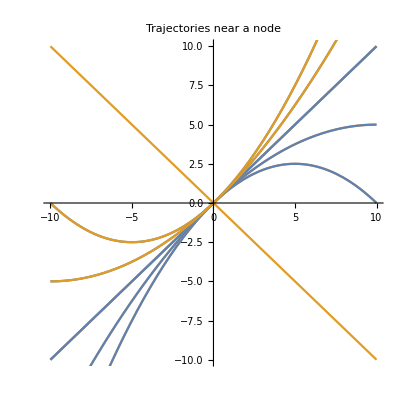

```mathematica
Show[{p1,p2,p3,p4,p5,p6},PlotLabel->"Trajectories near a node",AspectRatio->Automatic,PlotRange->{-10,10}]
```

## 4.4 Proper Node, Saddle Point, Center, Spiral Point

```mathematica
A={{1,0},{0,-1}};MatrixForm[A]
```

(1 | 0
0 | -1)

```mathematica
q=Det[A]
```

-1

```mathematica
Eigenvalues[A]
```

{-1,1}

```mathematica
A={{0,1},{-4,0}};MatrixForm[A]
```

(0 | 1
-4 | 0)

```mathematica
q=Det[A]
```

4

```mathematica
Eigenvalues[A]
```

{2 ⅈ,-2 ⅈ}

```mathematica
A={{-1,1},{-1,-1}};MatrixForm[A]
```

(-1 | 1
-1 | -1)

```mathematica
delta=(-2)^2-4Det[A]
```

-4

```mathematica
Eigenvalues[A]
```

{-1+ⅈ,-1-ⅈ}

## 4.5 Pendulum Equation

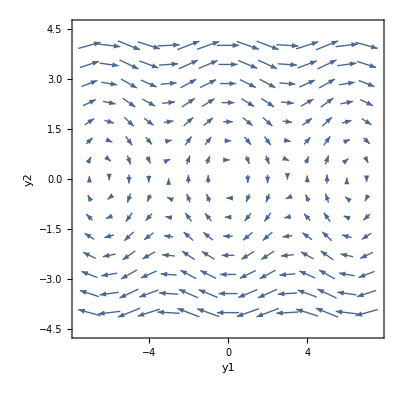

```mathematica
VectorPlot[{y2,-Sin[y1]},{y1,-7,7},{y2,-4,4},Axes->True,Ticks->{{-2Pi,-Pi,Pi,2Pi},Automatic},AxesLabel->{y1,y2}]
```

## 4.6 Nonhomogeneous System

```mathematica
Clear[y1,y2]
```

```mathematica
sys={y1'[t]==2y1[t]-4y2[t]+2t^2+10t,y2'[t]==y1[t]-3y2[t]+t^2+9t+3}
```

{y1'[t]==10 t+2 t^2+2 y1[t]-4 y2[t],y2'[t]==3+9 t+t^2+y1[t]-3 y2[t]}

```mathematica
sol=DSolve[sys,{y1[t],y2[t]},t]
```

{{y1[t]→-4/9 ⅇ^(-3 t) (-1+ⅇ^(3 t)) t (-3-t+ⅇ^(3 t) (12+t))+1/9 ⅇ^(-3 t) (-1+4 ⅇ^(3 t)) t (-4 (3+t)+ⅇ^(3 t) (12+t))+1/3 ⅇ^(-2 t) (-1+4 ⅇ^(3 t)) C[1]-4/3 ⅇ^(-2 t) (-1+ⅇ^(3 t)) C[2],y2[t]→-1/9 ⅇ^(-3 t) (-4+ⅇ^(3 t)) t (-3-t+ⅇ^(3 t) (12+t))+1/9 ⅇ^(-3 t) (-1+ⅇ^(3 t)) t (-4 (3+t)+ⅇ^(3 t) (12+t))+1/3 ⅇ^(-2 t) (-1+ⅇ^(3 t)) C[1]-1/3 ⅇ^(-2 t) (-4+ⅇ^(3 t)) C[2]}}

```mathematica
FullSimplify[%]
```

{{y1[t]→-t^2-1/3 ⅇ^(-2 t) (C[1]-4 C[2])+4/3 ⅇ^t (C[1]-C[2]),y2[t]→1/3 (9 t-ⅇ^(-2 t) (C[1]-4 C[2])+ⅇ^t (C[1]-C[2]))}}

```mathematica
A={{2,-4},{1,-3}}
```

{{2,-4},{1,-3}}

```mathematica
e=Eigensystem[A]
```

{{-2,1},{{1,1},{4,1}}}

```mathematica
yhom=c1 e[[2,1]]Exp[e[[1,1]]t]+c2 e[[2,2]]Exp[e[[1,2]]t]
```

{c1 ⅇ^(-2 t)+4 c2 ⅇ^t,c1 ⅇ^(-2 t)+c2 ⅇ^t}

## 4.7 Method of Undetermined Coefficients

```mathematica
A={{2,-4},{1,-3}}
```

{{2,-4},{1,-3}}

```mathematica
g={2t^2+10t,t^2+9t+3}
```

{10 t+2 t^2,3+9 t+t^2}

```mathematica
u={u1,u2};v={v1,v2};w={w1,w2};
```

```mathematica
yp=u+v t+w t^2
```

{u1+t v1+t^2 w1,u2+t v2+t^2 w2}

```mathematica
sys=D[yp,t]==A.yp+g
```

{v1+2 t w1,v2+2 t w2}=={10 t+2 t^2+2 (u1+t v1+t^2 w1)-4 (u2+t v2+t^2 w2),3+9 t+t^2+u1+t v1+t^2 w1-3 (u2+t v2+t^2 w2)}

```mathematica
eq1=sys/.t->0
```

{v1,v2}=={2 u1-4 u2,3+u1-3 u2}

```mathematica
eq2=sys/.t->1
```

{v1+2 w1,v2+2 w2}=={12+2 (u1+v1+w1)-4 (u2+v2+w2),13+u1+v1+w1-3 (u2+v2+w2)}

```mathematica
eq3=sys/.t->-1
```

{v1-2 w1,v2-2 w2}=={-8+2 (u1-v1+w1)-4 (u2-v2+w2),-5+u1-v1+w1-3 (u2-v2+w2)}

```mathematica
sol=Solve[{eq1,eq2,eq3},{u1,u2,v1,v2,w1,w2}]
```

{{u1→0,u2→0,v1→0,v2→3,w1→-1,w2→0}}

```mathematica
answer=yp/.sol
```

{{-t^2,3 t}}

## ----------------------The End----------------------